```mathematica
data=Cases[Import["/Users/kirillivanov/Documents/Файлы ТеХ/labs/342/3.4.2.xlsx"]⟦1,All,2;;⟧,Except[{"Таблица 1"|"",""..}]]
```

{{,T_в,dU,T_o,\sigmaT,\tau,Tdif,Trev,\sigmadif,\sigmarev},{1.,14.23,0.001,14.254,0.104065,7.937,14.605,0.0684696,0.15874,0.000744187},{2.,16.12,-0.017,15.712,0.104065,7.872,13.5774,0.0736516,0.15744,0.000854042},{3.,18.12,-0.018,17.688,0.104065,7.755,11.7491,0.085113,0.1551,0.00112358},{4.,20.1,-0.018,19.668,0.104065,7.568,8.88368,0.112566,0.15136,0.0019179},{5.,22.1,-0.017,21.692,0.104065,7.358,5.74922,0.173937,0.14716,0.00445217},{6.,24.11,-0.018,23.678,0.104065,7.193,3.3483,0.298659,0.14386,0.0128319},{7.,26.08,-0.018,25.648,0.104065,7.121,2.3177,0.431463,0.14242,0.0265129},{8.,28.1,-0.012,27.812,0.104065,7.079,1.7213,0.580957,0.14158,0.0477849},{9.,30.09,-0.017,29.682,0.104065,7.055,1.38208,0.723547,0.1411,0.0738687},{10.,32.08,-0.018,31.648,0.104065,7.036,1.11435,0.897383,0.14072,0.113321},{11.,34.08,-0.017,33.672,0.104065,7.022,0.91754,1.08987,0.14044,0.13},{12.,36.09,-0.019,35.634,0.104065,7.013,0.791225,1.26386,0.14026,0.152},{13.,38.08,-0.018,37.648,0.104065,7.005,0.679081,1.47258,0.1401,0.185},{14.,40.08,-0.019,39.624,0.104065,6.999,0.595057,1.68051,0.13998,0.211}}

```mathematica
data//TableForm
```

| T_в | dU | T_o | \sigmaT | \tau | Tdif | Trev | \sigmadif | \sigmarev
1. | 14.23 | 0.001 | 14.254 | 0.104065 | 7.937 | 14.605 | 0.0684696 | 0.15874 | 0.000744187
2. | 16.12 | -0.017 | 15.712 | 0.104065 | 7.872 | 13.5774 | 0.0736516 | 0.15744 | 0.000854042
3. | 18.12 | -0.018 | 17.688 | 0.104065 | 7.755 | 11.7491 | 0.085113 | 0.1551 | 0.00112358
4. | 20.1 | -0.018 | 19.668 | 0.104065 | 7.568 | 8.88368 | 0.112566 | 0.15136 | 0.0019179
5. | 22.1 | -0.017 | 21.692 | 0.104065 | 7.358 | 5.74922 | 0.173937 | 0.14716 | 0.00445217
6. | 24.11 | -0.018 | 23.678 | 0.104065 | 7.193 | 3.3483 | 0.298659 | 0.14386 | 0.0128319
7. | 26.08 | -0.018 | 25.648 | 0.104065 | 7.121 | 2.3177 | 0.431463 | 0.14242 | 0.0265129
8. | 28.1 | -0.012 | 27.812 | 0.104065 | 7.079 | 1.7213 | 0.580957 | 0.14158 | 0.0477849
9. | 30.09 | -0.017 | 29.682 | 0.104065 | 7.055 | 1.38208 | 0.723547 | 0.1411 | 0.0738687
10. | 32.08 | -0.018 | 31.648 | 0.104065 | 7.036 | 1.11435 | 0.897383 | 0.14072 | 0.113321
11. | 34.08 | -0.017 | 33.672 | 0.104065 | 7.022 | 0.91754 | 1.08987 | 0.14044 | 0.13
12. | 36.09 | -0.019 | 35.634 | 0.104065 | 7.013 | 0.791225 | 1.26386 | 0.14026 | 0.152
13. | 38.08 | -0.018 | 37.648 | 0.104065 | 7.005 | 0.679081 | 1.47258 | 0.1401 | 0.185
14. | 40.08 | -0.019 | 39.624 | 0.104065 | 6.999 | 0.595057 | 1.68051 | 0.13998 | 0.211

```mathematica
grids[dist_]:=Table[If[OddQ@Round@(i/dist),{i,Dashed},{i}],{i,Ceiling@(#1/dist)*dist,Floor@(#2/dist)*dist,dist}]&;
```

```mathematica
Needs@"ErrorBarPlots`";
vertSize=0.15;horizSize=0.03;
vertCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1+vertSize,#2},{#1-vertSize,#2}}&@@@{coord1,coord2})};
horizCross[coord1_,coord2_]:={Line@{coord1,coord2},Line/@({{#1,#2+horizSize},{#1,#2-horizSize}}&@@@{coord1,coord2})};
```

```mathematica
forFit=(*Select[*)data⟦2;;,{4,8}⟧(*,First@#>22&]*);
fit=LinearModelFit[forFit(*⟦All,;;2⟧*),{x,1},x];
forFit
fit@"ParameterTable"
fit@"Function"
```

{{14.254,0.0684696},{15.712,0.0736516},{17.688,0.085113},{19.668,0.112566},{21.692,0.173937},{23.678,0.298659},{25.648,0.431463},{27.812,0.580957},{29.682,0.723547},{31.648,0.897383},{33.672,1.08987},{35.634,1.26386},{37.648,1.47258},{39.624,1.68051}}

| Estimate | Standard Error | t-Statistic | P-Value
x | 0.0654603 | 0.00468218 | 13.9807 | 8.66628×10^-9
1 | -1.10954 | 0.130562 | -8.49817 | 2.01507×10^-6

-1.10954+0.0654603 #1&

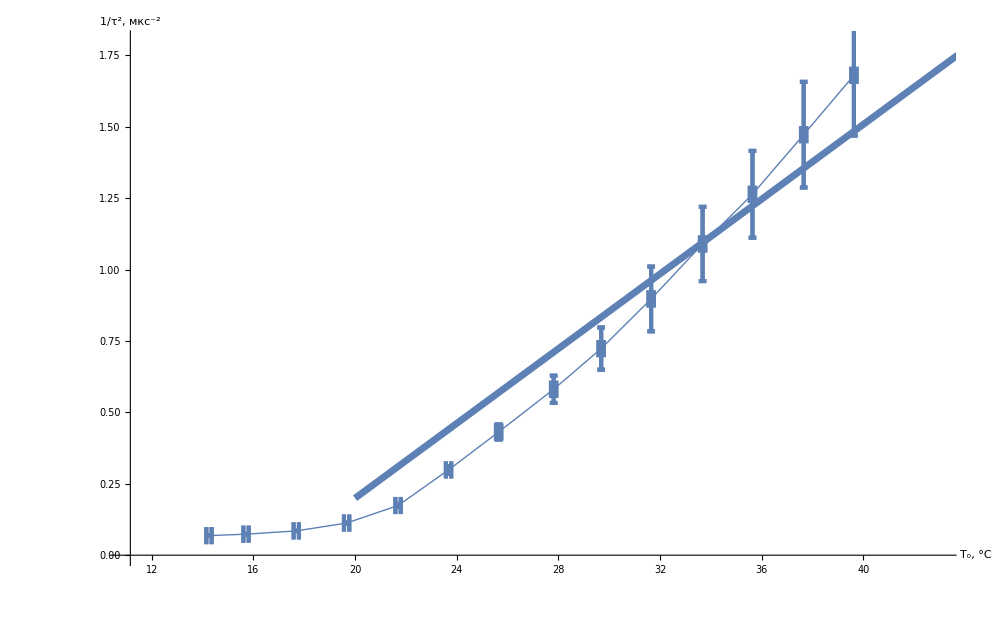

```mathematica
Show[ErrorListPlot[{{#1,#2},ErrorBar@##3}&@@@data⟦2;;,{4,8,5,10}⟧,
GridLines->{grids@1,grids@0.2},
AxesLabel->(Style[#,Bold,Black,Large]&)/@{"T_o, °C","1/τ^2, (:043c:043a:0441)^-2"},
AxesStyle->Directive[Large,Black],
ErrorBarFunction->Function[{coords,errors},{Thickness@0.003,vertCross@@({{#1,#2+errors⟦2,1⟧},{#1,#2+errors⟦2,2⟧}}&@@coords),horizCross@@({{#1+errors⟦1,1⟧,#2},{#1+errors⟦1,2⟧,#2}}&@@coords)}],
PlotMarkers->{Automatic,0.01},Joined->True,PlotStyle->Thickness@0.001,
PlotRange->{{11,43},{0,1.8}},
ImageSize->1000],Plot[fit["Function"]@x,{x,20,45}, PlotStyle->Thickness@0.005]]
```

```mathematica
data//TeXForm
```